# Audio to Image

Rongzhong Li, Feb 28, 2013

```mathematica
Exit
```

```mathematica
name="mario";
ampdat=Import[StringJoin[{NotebookDirectory[],name,"/",name,"_amp.dat"}],"Table"];
freqdat=Import[StringJoin[{NotebookDirectory[],name,"/",name,"_dct.dat"}],"Table"];
{time,freq}=Dimensions[freqdat]
c=2^(1/12);a=110;
```

{968,550}

### Sort

```mathematica
Histogram[Flatten[freqdat],Automatic,"Probability"]
ListLinePlot[Flatten[ampdat],ColorFunction->"Rainbow"]
```

### PitchTable

```mathematica
A3=Plot[12,{x,a,a c^12}];A4=Plot[24,{x,a,a c^24}];A5=Plot[36,{x,a,a c^36}];A6=Plot[48,{x,a,a c^48}];
Fs=ListPlot[Table[{a c^n,n},{n,48}],Filling->Axis];
Fruler=Show[Fs,A3,A4,A5,A6,AxesOrigin->{a,0}]
```

### Rescale Frequency Amplitude

```mathematica
rescaleF[min_,max_]:=(temp=(freqdat-min)*1/(max-min);freqdat=Table[If[temp[[t,f]]<0,0,If[temp[[t,f]]>1,1,temp[[t,f]]]],{t,time},{f,freq}];)
rescaleF[0.32,0.34];
Histogram[Flatten[freqdat],Automatic,"Probability"]
```

### Quick Preview

```mathematica
barps=16;
timetick=Table[{t,t/barps},{t,0,time,20barps}];
freqtick=Table[{2a c^(12i)/barps,a c^(12i)},{i,5}];pitchname=Table[{2a c^(12i)/barps,StringJoin[{"A",ToString[i+2]}]},{i,5}];
MatrixPlot[Transpose[freqdat],ColorFunction->"Rainbow",(*Mesh->{Transpose[freqtick][[1]],None},*)FrameTicks->{{freqtick,pitchname},{timetick,None}},FrameLabel->{{"Time (S)",None},{"Frequency (Hz)","Note Name"}},LabelStyle->Medium]
```

### Frequency ->Radius & Brightness, Frequency Amplitude -> Visible Spectrum-> Saturation.

```mathematica
range=ColorData["VisibleSpectrum","Range"];
r=range[[2]]-range[[1]];
clrF[f_,t_]:=(c=Ceiling[f/freq*r];dark=freqdat[[t,f]];
Darker[ColorData["VisibleSpectrum"][c+range[[1]]],1-dark])
Graphics[Table[{clrF[f,t],Point[{t,freq-f+1}]},{t,time},{f,freq}]]
```

$Aborted

```mathematica
clrF[f_,t_]:=(c=Ceiling[freqdat[[t,f]]*r];dark=f/freq;
Darker[ColorData["VisibleSpectrum"][c+range[[1]]],1-dark])
Graphics[Table[{clrF[f,t],Point[{t,freq-f+1}]},{t,time},{f,freq}]]
```

```mathematica
barps=16;
range=ColorData["VisibleSpectrum","Range"];
r=range[[2]]-range[[1]];
clrF[f_,t_]:=(c=Ceiling[freqdat[[t,f]]*r];dark=f/freq;
Darker[ColorData["VisibleSpectrum"][c+range[[1]]],1-dark])
```

```mathematica
g=Graphics[{Table[{clrF[f,t],Disk[f{Sin[2Pi  t/time],Cos[2Pi t/time]},1Pi f/time]},{t,time},{f,freq,1,-1}],{Red,Rectangle[0.8{-freq,-freq},{-freq,-freq}]},{Green,Rectangle[0.8{-freq,freq},{-freq,freq}]},{Blue,Rectangle[0.8{freq,freq},{freq,freq}]},{Black,Rectangle[0.8{freq,-freq},{freq,-freq}]},Text[Style[StringJoin[{ToString[SetAccuracy[time/barps,3]]," s","\n",ToString[freq*barps/2],"Hz"}],Large,Bold,White],0.9{freq,-freq}]},PlotLabel->Style[name,Large]];
```

```mathematica
Export[StringJoin[{NotebookDirectory[],name,"\\",name,".png"}],g,"PNG",ImageSize->1024];
```

#### Data ⟹ Matrix

```mathematica
mat=Table[0,{i,2freq+1},{j,2freq+1}];
Dimensions[Table[mat[[freq+1+Round[f Sin[2Pi t/time]],freq+1+Round[f Cos[2Pi t/time]]]]=clrF[f,t],{t,time},{f,freq}]]
matplot=MatrixPlot[mat]
```

#### Matrix ⟸ Data

```mathematica
mat=Table[0,{i,2freq},{j,2freq}];
Table[{x=j-freq;y=freq-i;a=If[x>0,ArcCos[y/f],-ArcCos[y/f]];f=Round[√(y^2+x^2)]+1;t=Round[a/(2Pi)time]+1;mat[[i,j]]=If[f<freq,clrF[f+1,t],Which[i>(2-0.2)freq&&j<0.2freq,Red,i<0.2freq&&j<0.2freq,Green,i<0.2freq&&j>(2-0.2)freq,Blue,i>(2-0.2)freq&&j>(2-0.2)freq,Black,True,White]]},{i,2freq},{j,2freq}];
```

```mathematica
matplot=MatrixPlot[mat]
```

```mathematica
Graphics[{matplot,Inset[Text[Style[StringJoin[{ToString[SetAccuracy[time/barps,3]]," s","\n",ToString[freq*barps/2],"Hz"}],Large,Bold,White]],0.9{freq,-freq}]},PlotLabel->Style[name,Large]]
```

### Appendix

#### ColorMap (Hue)

```mathematica
MatrixPlot[Table[Hue[i/100,1,br/100],{i,100},{br,100}]]
```

#### ColorMap (Visible Spectrum)

Darker -> Brightness(larger,darker), Lighten -> Saturation(smaller,more)

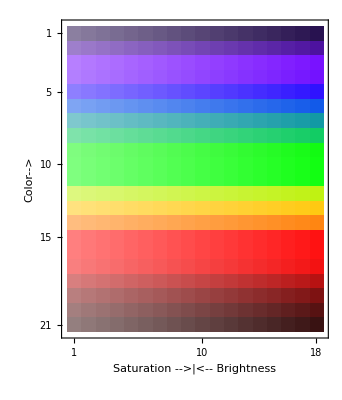

```mathematica
range=ColorData["VisibleSpectrum","Range"];
r=range[[2]]-range[[1]];
light=Table[Lighter[ColorData["VisibleSpectrum"][c+range[[1]]],0.5-s/r],{c,0,r,r/20},{s,1,r/2-r/20,r/40}];
dark=Table[Darker[ColorData["VisibleSpectrum"][c+range[[1]]],0.5-b/r],{c,0,r,r/20},{b,r/2+r/20,1,r/40}];
indC=Transpose[Join[Transpose[light],Transpose[dark]]];
MatrixPlot[indC,FrameLabel->{"Color-->","Saturation -->|<-- Brightness"},LabelStyle->Medium]
```

```mathematica
ColorData["Rainbow"]
```

ColorDataFunction[{0,1},-Graphics-]

```mathematica
ColorData["VisibleSpectrum"]
```

ColorDataFunction[{380,750},-Graphics-]